# AC learning for line bundles

## Load packages

```mathematica
<<LineBundleEnv`
```

LineBundleEnv: RL Environment for line bundles on CY manifolds

Execute ?LineBundleEnv for help. Current LineBundleEnv options:

{CicyNum→7884,NumPs→2,Conf→{{3},{3}},c2TX→{36,36},IntersecNumbers→{{{0,3},{3,3}},{{3,3},{3,0}}},TargetIndex→18,EntryRange→{-7,8},BoundaryPenalty→-1,TerminalBonus→2,RewardOffset→-1,StepPenalty→0,NumBits→4}

```mathematica
<<ActorCritic`
SetOptions[ActorCritic,"InitModule"->LineBundleEnv`LineBundleInit,"ActModule"->LineBundleEnv`LineBundleAct,"EnvironmentOptions"->LineBundleEnv`LineBundleEnv];
```

ActorCritic: policy-based RL algorithm

Execute ?ActorCritic for help

{InitModule→LineBundleEnv`LineBundleInit,ActModule→LineBundleEnv`LineBundleAct,StateDim→2,ActionDim→4,NAgents→4,EnvironmentOptions→LineBundleEnv`LineBundleEnv,ActionForm→Probabilities}

## Training

### bicubic, targetind=18

```mathematica
SetOptions[ActorCritic,"StateDim"->2,"ActionDim"->4]
```

{InitModule→LineBundleInit,ActModule→LineBundleAct,StateDim→2,ActionDim→4,NAgents→4,EnvironmentOptions→LineBundleEnv,ActionForm→Probabilities}

```mathematica
SetOptions[LineBundleEnv,"StepPenalty"->-1]
```

{CicyNum→7884,NumPs→2,Conf→{{3},{3}},c2TX→{36,36},IntersecNumbers→{{{0,3},{3,3}},{{3,3},{3,0}}},TargetIndex→18,EntryRange→{-7,8},BoundaryPenalty→-1,TerminalBonus→2,RewardOffset→-1,StepPenalty→-1,NumBits→4}

```mathematica
pnet={8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"]};
vnet={8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"],8,ElementwiseLayer["SELU"]};
```

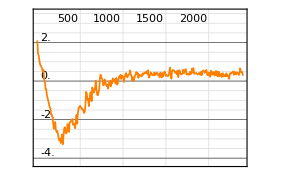
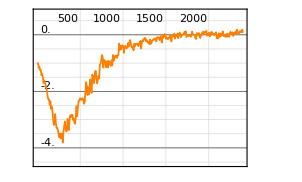
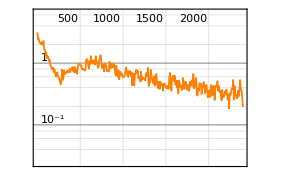
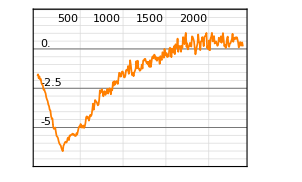
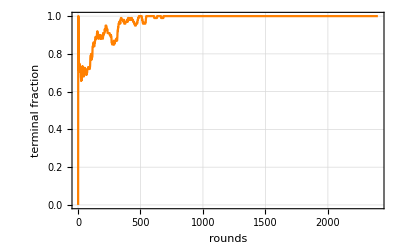
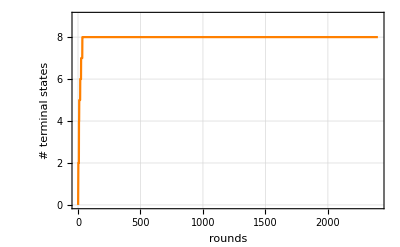
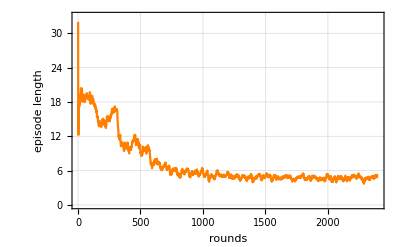
{ | rounds
loss | -Graphics-, | rounds
PolicyLoss | -Graphics-, | rounds
ValueLoss | -Graphics-, | rounds
TDReturn | -Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
res=ReLearn[Method->{"ADAM","LearningRate"->1/1000},MaxTrainingRounds->5000,BatchSize->32,"Gamma"->0.8,"PolicyNet"->pnet,"ValueNet"->vnet];
{res["Loss"],res["PolicyLoss"],res["ValueLoss"],res["TDReturn"],res["FracTerminal"],res["NTerminal"],res["AvEpisodeLength"]}
```

```mathematica
Put[res,NotebookDirectory[]<>"networks/acnet7884_target18"];
```

## Analyse

### bicubic, targetind=18

Basic characteristics of trained network

```mathematica
SetOptions[ActorCritic,"StateDim"->2,"ActionDim"->4]
```

{InitModule→LineBundleInit,ActModule→LineBundleAct,StateDim→2,ActionDim→4,NAgents→4,EnvironmentOptions→LineBundleEnv,ActionForm→Probabilities}

```mathematica
res=Get[NotebookDirectory[]<>"networks/acnet7884_target18"];
res["FullNet"]
res["EnvironmentOptions"]
{res["Loss"],res["PolicyLoss"],res["ValueLoss"],res["TDReturn"],res["FracTerminal"],res["NTerminal"]}
res["TerminalStates"]
```

NetGraph[<>]

{CicyNum→7884,NumPs→2,Conf→{{3},{3}},c2TX→{36,36},IntersecNumbers→{{{0,3},{3,3}},{{3,3},{3,0}}},TargetIndex→18,EntryRange→{-7,8},BoundaryPenalty→-1,TerminalBonus→2,RewardOffset→-1,StepPenalty→-1,NumBits→4}

{ | rounds
loss | -Graphics-, | rounds
PolicyLoss | -Graphics-, | rounds
ValueLoss | -Graphics-, | rounds
TDReturn | -Graphics-,-Graphics-,-Graphics-}

{<|Input→{1,2},Terminal→True,Value→0.|>,<|Input→{2,1},Terminal→True,Value→0.|>,<|Input→{0,6},Terminal→True,Value→0.|>,<|Input→{1,-5},Terminal→True,Value→0.|>,<|Input→{-4,2},Terminal→True,Value→0.|>,<|Input→{-5,1},Terminal→True,Value→0.|>,<|Input→{6,0},Terminal→True,Value→0.|>,<|Input→{2,-4},Terminal→True,Value→0.|>}

Fraction of terminal states and average episode length

```mathematica
nterm=0;eplen=0;nep=100;
Monitor[For[i=1,i≤nep,i++,
instate=LineBundleInit[];
ep=Episode[instate,"PolicyNet"->res["PolicyNet"],"MaxEpisodeLength"->32,"PolicyType"->"probabilistic"];
If[ep["Terminal"],nterm++;eplen=eplen+Length[ep["Input"]]]],i];
{nterm,eplen}/nep//N
```

{0.91,11.04}

find all terminal states

```mathematica
isec="IntersecNumbers"/.Options[LineBundleEnv];c2TX="c2TX"/.Options[LineBundleEnv];
targetind="TargetIndex"/.Options[LineBundleEnv];
lb={Subscript[k, 1],Subscript[k, 2]}; ind=isec.lb.lb.lb/6+c2TX.lb/12//Simplify
sollst={Subscript[k, 1],Subscript[k, 2]}/.Solve[ind==targetind,{Subscript[k, 1],Subscript[k, 2]},Integers]
```

3/2 (2 k_2+k_1^2 k_2+k_1 (2+k_2^2))

{{-5,1},{-4,2},{0,6},{1,-5},{1,2},{2,-4},{2,1},{6,0}}

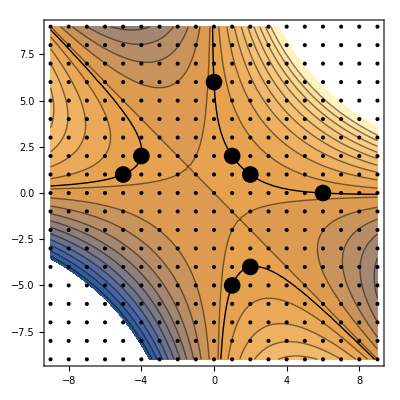

```mathematica
plot7884=Show[ContourPlot[ind,{Subscript[k, 1],-9,9},{Subscript[k, 2],-9,9},Frame->True,Contours->20,PlotRange->{{-9,9},{-9,9}}],
ContourPlot[ind==targetind,{Subscript[k, 1],-9,9},{Subscript[k, 2],-9,9},Frame->True,ContourStyle->{Black,Thick}],
ListPlot[Flatten[Table[{i,j},{i,-9,9},{j,-9,9}],1],PlotStyle->Black],
ListPlot[sollst,PlotStyle->{Black,PointSize[0.03]}]]
```

Example episodes

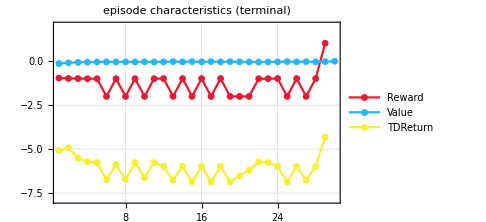

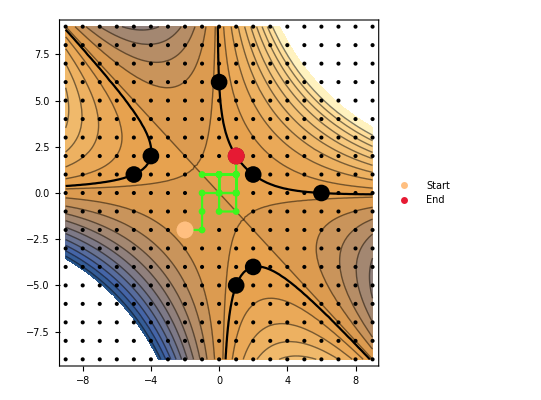

```mathematica
instate=CompleteState[{-2,-2}];
ep=Episode[instate,"FullNet"->res["FullNet"],"MaxEpisodeLength"->32,"PolicyType"->"probabilistic"];
plots=PlotEpisode[ep,"PlotLst"->{1,2,3},"Projection"->{{1,0},{0,1}},"Labels"->False];
plots["Rewards"]
Show[plot7884,plots["States"]]
```

Basins of attraction

{{1,2},{2,1},{0,6},{1,-5},{-4,2},{-5,1},{6,0},{2,-4}}

{99,92,9,7,13,13,43,4}

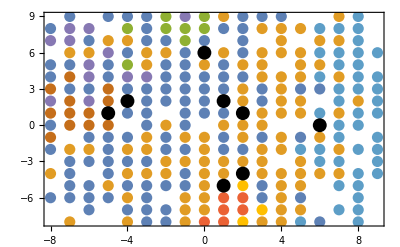

```mathematica
pts=Flatten[Table[{i,j},{i,-9,9},{j,-9,9}],1];
tslst=Map[#["Input"]&,res["TerminalStates"]]
domains=Table[{},{Length[tslst]}];
For[i=1,i≤Length[pts],i++,
in=CompleteState[pts[[i]]];
ep=Episode[in,"PolicyNet"->res["PolicyNet"],"MaxEpisodeLength"->32,"PolicyType"->"probabilistic"];
If[ep["Terminal"],ts=Last[ep["Input"]];pos=Position[tslst,ts][[1,1]];domains[[pos]]=Append[domains[[pos]],pts[[i]]]]];
Map[Length,domains]
Show[ListPlot[DeleteCases[domains,{}],Frame->True,PlotStyle->PointSize[0.02]],ListPlot[tslst,PlotStyle->{Black,PointSize[0.025]}]]
```